## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
<<"Definitions/Teukolsky.wl"
<<"Definitions/SWSH.wl"
```

## Equation and and Eigenvalue function

```mathematica
Eq=EqTeukolskyRadial/.RuleKRadial;
```

```mathematica
Clear@ℰ;
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real?Negative]:=ℰ[𝓈,ℓ,-𝓂,-𝒸];
ℰ[𝓈_Integer?Negative,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]:=ℰ[-𝓈,ℓ,𝓂,𝒸];
ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]/;ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=SpinWeightedSpheroidalHarmonicEigenvalue[𝓈,ℓ,𝓂,N@𝒸];
(*ℰ[𝓈_Integer,ℓ_Integer?NonNegative,𝓂_Integer,𝒸_Real]/;ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=(Simplify[SWSHEigenCoef//.Rule𝒽∪Ruleκpm∪{s->𝓈,m->𝓂}]/.l->ℓ).Table[𝒸^(i-1),{i,Length@SWSHEigenCoef}];*)
```

## Parameter rules and equation simplification

```mathematica
RuleRHorizon={R->Function[x,x^(-s-I χ/τ)f[x]]};
EquationF=PowerExpand@Simplify[x^(s+I χ/τ)x (x+τ) (Eq/.RuleRHorizon)];
(* all params *)
RuleBoundaryBH={𝒶[0]->1,𝒷[0]->(-ℬ τ^2)/(4 (ⅈ τ/2+χ) χ)};
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),ℬ->Sqrt[(λ+(s+1)s)^2-4((𝒥 ω̄)/rp)^2+4m (𝒥 ω̄)/rp],  
λ->((𝒥 ω̄)/rp)^2-2m((𝒥 ω̄)/rp)+ℰ[s,l,m,(𝒥 ω̄)/rp]-s(s+1)};
```

```mathematica
(* Function to replace all parameters accordingly *)
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_]=#1//.RuleParams∪{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}&;
ReplaceParams[𝒿_,𝓈_,ℓ_,𝓂_,𝓌_]=#1//.RuleParams∪{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿,ω̄->𝓌}&;
```

## Equation solver definition

```mathematica
(* Coeficients to estimate f and f' close to BH horizon *)
nCoefH=6;
RuleFHorizon={f->Function[x,∑_(n=0)^nCoefH 𝒶[n] x^n]};
```

```mathematica
(* Coeficients to estimate Ain and Aout at infinity *)
nCoefInf=10;
RuleRinInf={R->Function[x,ⅇ^(-ⅈ ω̄ x)x^(-1-ⅈ ω̄ (2-τ)) ∑_(n=0)^nCoefInf 𝒾[n] x^-n]};
RuleRoutInf={R->Function[x, ⅇ^(ⅈ ω̄ x)x^(-1-2 s+ⅈ ω̄ (2-τ)) ∑_(n=0)^nCoefInf ℴ[n] x^-n]};
```

```mathematica
(* OptionsPattern to use with SolveωF to get more precision/accuracy out of NDSolve *)
IncreasePrecision={PrecisionGoal->10,AccuracyGoal->60,MaxSteps->10^8};
```

```mathematica
(* Information to include on CSV headers *)
metaRule={"xH"->10^(-12.),"fpH"->"1.0","fmH"->"1.0","nCoefH"->nCoefH,"nCoefInf"->nCoefInf};
headerZMetaRule={"headers"->{"J/M^2","omega*rp","Zphi0","Zphi2","Zphi0phi2"}};
headerϕMetaRule={"headers"->{"J/M^2","omega*rp","RE(Yin/Yhole)","IM(Yin/Yhole)","RE(Zout/Zhole)","IM(Zout/Zhole)"}};
headerϕ0MetaRule={"headers"->{"J/M^2","omega*rp","RE(Yin/Yhole)","IM(Yin/Yhole)","RE(Yout/Yhole)","IM(Yout/Yhole)"}};
headerϕ2MetaRule={"headers"->{"J/M^2","omega*rp","RE(Zin/Zhole)","IM(Zin/Zhole)","RE(Zout/Zhole)","IM(Zout/Zhole)"}};
```

#### Solver 1 (simpler)

```mathematica
Clear[SolveSingle];
SolveSingle[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝓌_?NumberQ,opts:OptionsPattern[]]/;0<𝒿<1&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Module[{x0,xINF,eqF,f0,fp0,fINF,ev},
(* almost 0. starting point, BH horizon / almost ∞, a lot of wave lenghts way from horizon *)
x0=10^-12.;
xINF=2 π/Abs[𝓌]*200.;
ev=ℰ[𝓈,ℓ,𝓂,(𝒿 𝓌)/(1+Sqrt[1-𝒿^2])];
{eqF,fINF}={EquationF,f[xINF] ⅇ^(ⅈ(Sign[𝓈] ω̄ (xINF+(2-τ)Log[xINF])-χ/τ Log[xINF]))}//ReplaceParams[𝒿,𝓈,l0,𝓂,𝓌];
{f0,fp0}={f[x0],f'[x0]}/.RuleFHorizon/.First@Solve[CoefficientList[eqF/.RuleFHorizon,x][[2;;nCoefH+1]]==0,Table[𝒶[n],{n,1,nCoefH}]//Evaluate];
{𝒿,𝓌,fINF}/.First@NDSolve[{eqF==0,f0==f[x0],fp0==f'[x0]}/.{ℰ[__]->ev,𝒶[0]->1},f,{x,x0,xINF},Sequence@@FilterRules[{opts}, Options[NDSolve]]]
];
```

#### Solver 2 (higher order corrections)

```mathematica
Clear[SolveBoth];
SolveBoth[𝒿_?NumberQ,𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝓌_?NumberQ,opts:OptionsPattern[]]/;0<𝒿<1&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
Module[{eqF,f0,fp0,coefInInf,coefOutInf,in,out,ev,x0,xINF},
(* almost 0. starting point, BH horizon / almost ∞, a lot of wave lenghts way from horizon *)
x0=10^-12.;
xINF=2Pi/Abs[𝓌]*80.;
ev=ℰ[𝓈,ℓ,𝓂,(𝒿 𝓌)/(1+Sqrt[1-𝒿^2])];
eqF=EquationF//ReplaceParams[𝒿,𝓈,l0,𝓂,𝓌];

{f0,fp0}={f[x0],f'[x0]}/.RuleFHorizon/.First@Solve[CoefficientList[eqF/.RuleFHorizon,x][[2;;nCoefH+1]]==0,Table[𝒶[n],{n,1,nCoefH}]//Evaluate];
coefInInf=First@Solve[0==Simplify@SeriesCoefficient[Series[ⅇ^(ⅈ ω̄ x) x^(ⅈ ω̄ (2-τ)) Eq/.RuleRinInf,{x,∞,nCoefInf}]//ReplaceParams[𝒿,𝓈,l,𝓂,𝓌],#]&/@Range[nCoefInf],Evaluate@Table[𝒾[n],{n,1,nCoefInf}]];
coefOutInf=First@Solve[0==Simplify@SeriesCoefficient[Series[ⅇ^(-ⅈ ω̄ x) x^(2 s-ⅈ ω̄ (2-τ)) Eq/.RuleRoutInf,{x,∞,nCoefInf}]//ReplaceParams[𝒿,𝓈,l,𝓂,𝓌],#]&/@Range[nCoefInf],Evaluate@Table[ℴ[n],{n,1,nCoefInf}]];
{in,out}=Total@ReplaceParams[𝒿,𝓈,l0,𝓂,𝓌][{R[x]/.RuleRinInf/.coefInInf,R[x]/.RuleRoutInf/.coefOutInf}]//{𝒾[0],ℴ[0]}/.First@Solve[{#==RInf,D[#,x]==RpInf}/.{x->xINF,ℰ[__]->ev},{𝒾[0],ℴ[0]}]&;
 
{𝒿,𝓌,in,out}/.ReplaceParams[𝒿,𝓈,l0,𝓂,𝓌][{RInf->R[xINF],RpInf->R'[xINF]}/.RuleRHorizon]/.First@NDSolve[{eqF==0,f0==f[x0],fp0==f'[x0]}/.{ℰ[__]->ev,𝒶[0]->1},f,{x,x0,xINF},Sequence@@FilterRules[{opts}, Options[NDSolve]]]
];
```

## Analysis

### Large ℓ=40, varying 0<𝒿<1 and azimuthal number 𝓂

```mathematica
g=If[#>0,#-2Pi,#]&;
```

```mathematica
rng=Range[0.01,0.99,0.04]∪{0.98,0.99,0.999,0.9999};
```

```mathematica
test1=ParallelTable[ReplaceParams[𝒿,-1,40,1,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,1,0.4,IncreasePrecision],{𝒿,rng}];
```

```mathematica
test2=ParallelTable[ReplaceParams[𝒿,-1,40,0,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,0,0.4,IncreasePrecision],{𝒿,rng}];
```

```mathematica
test3=ParallelTable[ReplaceParams[𝒿,-1,40,-1,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,-1,0.4,IncreasePrecision],{𝒿,rng}];
```

```mathematica
test4=ParallelTable[ReplaceParams[𝒿,-1,40,7,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[𝒿,-1,40,7,0.4,IncreasePrecision],{𝒿,rng}];
```

FittedModel[-2.72831-(3.50601 x^2)/((1+√(1-x^2))^2)]

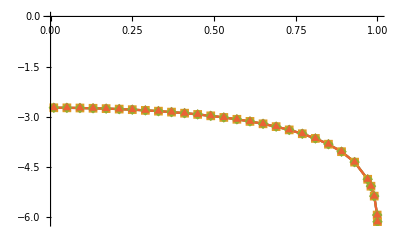

```mathematica
data1={rng[[#]],((Arg@test1[[#,3]]+If[Arg@test1[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
data2={rng[[#]],((Arg@test2[[#,3]]+If[Arg@test2[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
data3={rng[[#]],((Arg@test3[[#,3]]+If[Arg@test3[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
data4={rng[[#]],((Arg@test4[[#,3]]+If[Arg@test4[[#,3]]>0,-2Pi,0]))}&/@Range@Length@rng;
nlmf=NonlinearModelFit[data1,α+(β x^2)/(4(1+√(1-x^2))^2),{α,β,γ},x]
dataA={#,nlmf[#]}&/@rng;
{data1,data2,data3,data4}//ListPlot[#,Joined->True,PlotRange->All,PlotMarkers->Automatic]&
```

### Phases behaviour for |s|<ℓ<40

```mathematica
spin0=ParallelTable[ReplaceParams[j,-1,ℓ,1,0.4]@{j,l,1,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[j,-1,ℓ,1,0.4,{PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8}],{j,0.01,0.96,0.05},{ℓ,30,30}]//Flatten[#,1]&;
```

```mathematica
spin1=ParallelTable[ReplaceParams[j,-1,ℓ,1,0.2]@{j,l,1,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[j,-1,ℓ,1,0.2,{PrecisionGoal->13,AccuracyGoal->70,MaxSteps->10^8}],{j,0.01,0.96,0.05},{ℓ,32,32}]//Flatten[#,1]&;
```

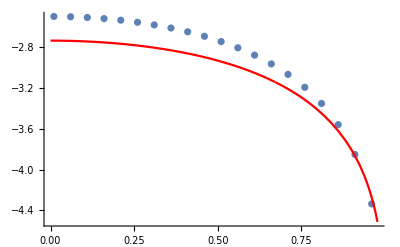

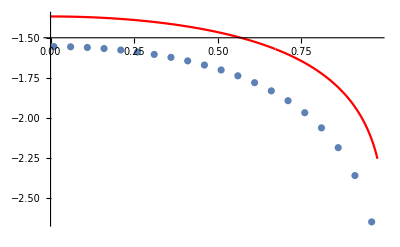

```mathematica
p1=ListPlot[{#1,g@Arg[#4]}&@@@spin0];
p3=ListPlot[{#1,g@Arg[#4]}&@@@spin1];
data0=ReplaceParams[#1,-1,30,1,0.4]@{#1,g@Arg[#4]-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ) I ω̄]]}&@@@spin0;
p2=Plot[g@ReplaceParams[𝒿,-1,30,1,0.4][Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ) I ω̄]]],{𝒿,0,1},PlotStyle->Red];
p4=Plot[g@ReplaceParams[𝒿,-1,30,1,0.2][Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ) I ω̄]]],{𝒿,0,1},PlotStyle->Red];
Show[p1,p2,PlotRange->All]
Show[p3,p4,PlotRange->All]
```

#### Fitting 1

```mathematica
modes1=ParallelTable[ReplaceParams[0.9,-1,ℓ,𝓂,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.9,-1,ℓ,𝓂,0.4,IncreasePrecision],{ℓ,1,50},{𝓂,{-1,0,1}}];
```

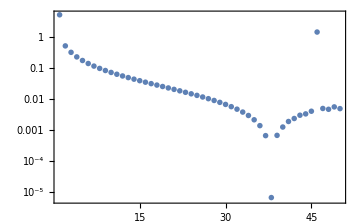
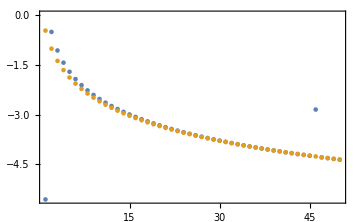
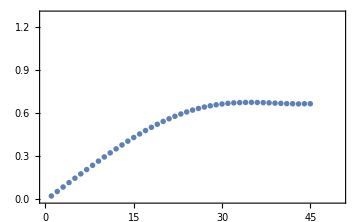
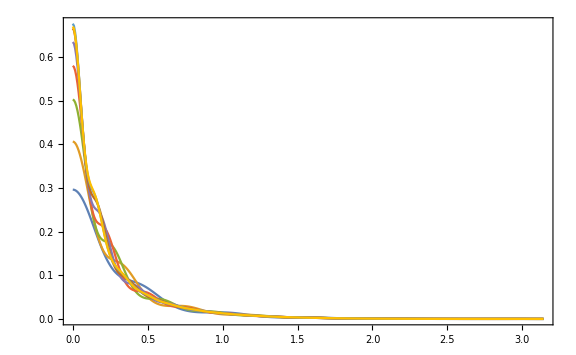
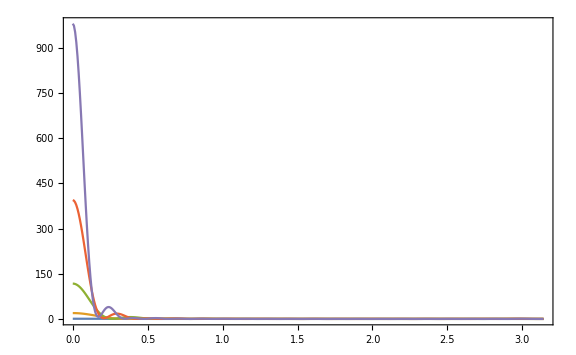
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- |  | -Graphics- |

```mathematica
δ1=0.0185;
dataV1=Last[Flatten[modes1,{2}]]⟦;;50⟧;
funcV1=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.9,-1,ℓ,1,0.4]@(dataV1⟦ℓ,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ1])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV1⟦All,1⟧}];
funcV1noreg=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.9,-1,ℓ,1,0.4]@(dataV1⟦ℓ,3⟧-1)SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV1⟦All,1⟧}];
argV1={{#1,g@Arg@#3}&@@@dataV1,ReplaceParams[0.9,-1,#1,1,0.4]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ1]]}&@@@dataV1}//ListPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
diffV1=ReplaceParams[0.9,-1,#1,1,0.4]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ1]]//Abs}&@@@dataV1//ListLogPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
sumV1={Range[0,Pi,Pi/400],Abs[Total@funcV1[[1;;#]]]^2}ᵀ&/@{10,14,18,22,26,30,34,40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
sumV1noreg={Range[0,Pi,Pi/400],Abs[Total@funcV1noreg[[1;;#]]]^2}ᵀ&/@{4,8,12,16,20}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
{{diffV1,argV1,ListPlot[First@(Abs[Total@funcV1[[1;;#]]]^2)&/@Range[50],ImageSize->Medium,Frame->True],SpanFromLeft},{sumV1,SpanFromLeft,sumV1noreg,SpanFromLeft}}//Grid[#,Alignment->Left]&
```

#### Fitting 2

```mathematica
modes2=ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.99,-1,ℓ,𝓂,0.4,IncreasePrecision],{ℓ,1,50},{𝓂,{1}}];
```

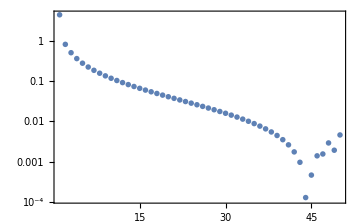
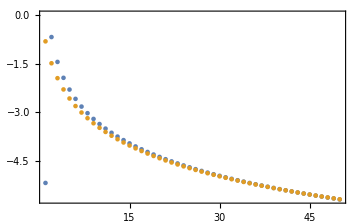
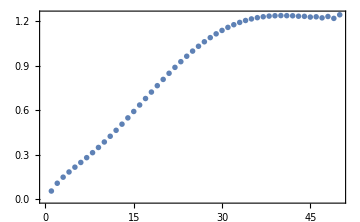
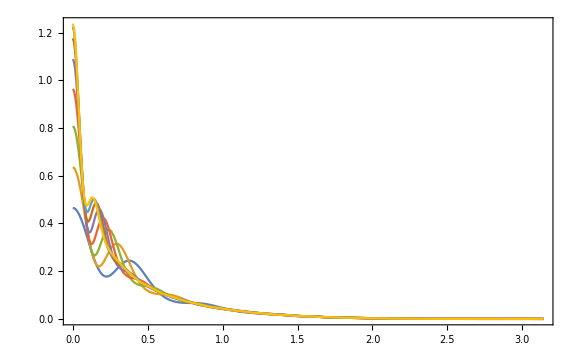
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
δ2=-0.181;
dataV2=Flatten[modes2,1][[;;50]];
funcV2=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,1,0.4]@(dataV2⟦ℓ,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ2])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV2⟦All,1⟧}];
argV2={{#1,g@Arg@#3}&@@@dataV2,ReplaceParams[0.99,-1,#1,1,0.4]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ2]]}&@@@dataV2}//ListPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
diffV2=ReplaceParams[0.99,-1,#1,1,0.4]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ2]]//Abs}&@@@dataV2//ListLogPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
sumV2={Range[0,Pi,Pi/400],Abs[Total@funcV2[[1;;#]]]^2}ᵀ&/@{12,16,20,24,28,32,36,40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
{{diffV2,argV2,ListPlot[First@(Abs[Total@funcV2[[1;;#]]]^2)&/@Range[50],ImageSize->Medium,Frame->True]},{sumV2,SpanFromLeft,SpanFromLeft}}//Grid
```

#### Fitting 3

```mathematica
modes3=ParallelTable[ReplaceParams[0.80,-1,ℓ,𝓂,0.3]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.80,-1,ℓ,𝓂,0.30,IncreasePrecision],{ℓ,1,50},{𝓂,{1}}];
```

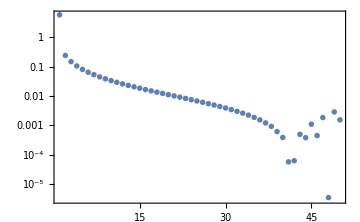
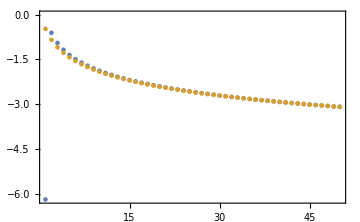
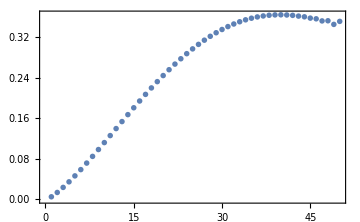
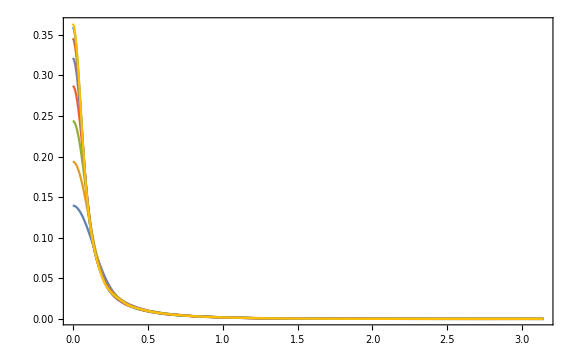
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
δ3=-0.148;
dataV3=Flatten[modes3,1];
funcV3=Table[#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.8,-1,ℓ,1,0.3]@(dataV3⟦ℓ,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ3])SpinWeightedSphericalHarmonicY[-1,1,1,0,0]SpinWeightedSphericalHarmonicY[-1,ℓ,1,0,0]*SpinWeightedSphericalHarmonicY[-1,ℓ,1,θ,0],{ℓ,dataV3⟦All,1⟧}];
argV3={{#1,g@Arg@#3}&@@@dataV3,ReplaceParams[0.8,-1,#1,1,0.3]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ3]]}&@@@dataV3}//ListPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
diffV3=ReplaceParams[0.8,-1,#1,1,0.3]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ3]]//Abs}&@@@dataV3//ListLogPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
sumV3={Range[0,Pi,Pi/400],Abs[Total@funcV3[[1;;#]]]^2}ᵀ&/@{12,16,20,24,28,32,36,40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
{{diffV3,argV3,ListPlot[First@(Abs[Total@funcV3[[1;;#]]]^2)&/@Range[50],ImageSize->Medium,Frame->True]},{sumV3,SpanFromLeft,SpanFromLeft}}//Grid
```

#### Fitting 4

```mathematica
modes4=ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@{l,m,(-1)^(l+1)(l(l+1))/(4 (ω̄)^2)#4/#3}&@@SolveBoth[0.99,-1,Sequence@@Echo[{ℓ,𝓂}],0.4,IncreasePrecision],{ℓ,1,40},{𝓂,-ℓ,ℓ}];
```

```mathematica
{0.99,0.4,#1,#2,Re@#3,Im@#3}&@@@Flatten[modes4,{1,2}]//Export["Zratio.csv",#]&
```

Zratio.csv

```mathematica
δ4=-0.18;
dataV4=modes4;
{θ0,ϕ0}={0.3,0};
funcV4pos=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ+𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,-1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
funcV4neg=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ-𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
```

```mathematica
funcV4pos0=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ+𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
funcV4neg0=ParallelTable[Total@#,{θ,0.,Pi,Pi/400.}]&/@ParallelTable[ReplaceParams[0.99,-1,ℓ,𝓂,0.4]@(dataV4⟦ℓ,ℓ-𝓂+1,3⟧-Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4])SpinWeightedSphericalHarmonicY[-1,1,-1,θ0,ϕ0]SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ0,ϕ0]*SpinWeightedSphericalHarmonicY[-1,ℓ,𝓂,θ,0],{ℓ,(First/@dataV4[[All,All,1]])},{𝓂,dataV4⟦ℓ,All,2⟧}];
```

```mathematica
sumV4={Range[0,Pi,Pi/400],Abs[Total@funcV4pos[[1;;#]]]^2+Abs[Total@funcV4neg[[1;;#]]]^2}ᵀ&/@{40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
sumV40={Range[0,Pi,Pi/400],Abs[Total@funcV4pos0[[1;;#]]]^2+Abs[Total@funcV4neg0[[1;;#]]]^2}ᵀ&/@{40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large,PlotStyle->Red]&;
```

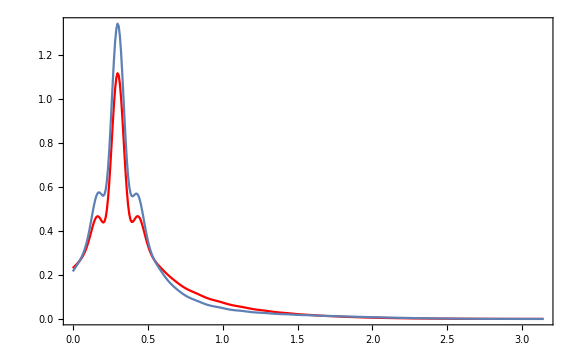

```mathematica
Show[sumV40,sumV4,PlotRange->All]
```

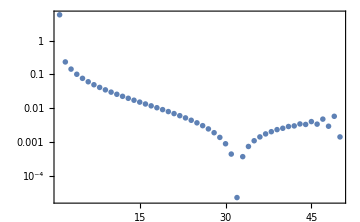
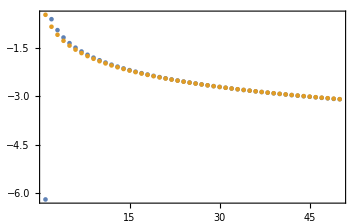
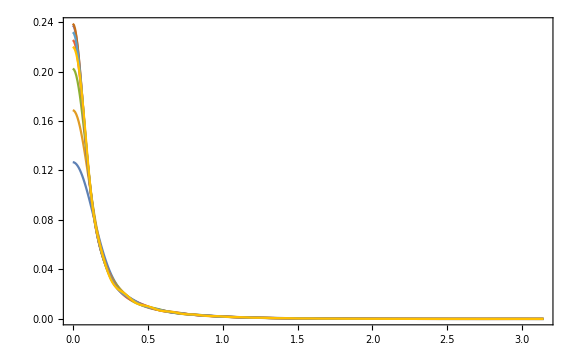
-Graphics- | -Graphics-
-Graphics- |

```mathematica
argV4={{#1,g@Arg@#3}&@@@dataV3,ReplaceParams[0.99,-1,#1,1,0.4]@{l,g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4]]}&@@@dataV4}//ListPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
diffV4=ReplaceParams[0.8,-1,#1,1,0.3]@{#1,g@Arg@#3-g@Arg[Gamma[l+1-(2-τ)I ω̄]/Gamma[l+1+(2-τ)I ω̄] Exp[I δ4]]//Abs}&@@@dataV4//ListLogPlot[#,Joined->False,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Medium]&;
sumV4={Range[0,Pi,Pi/400],Abs[Total@funcV4[[1;;#]]]^2}ᵀ&/@{12,16,20,24,28,32,36,40}//ListPlot[#,Joined->True,PlotRange->All,Frame->True,PlotRangePadding->Scaled[0.01],ImageSize->Large]&;
{{diffV4,argV4},{sumV4,SpanFromLeft}}//Grid
```

## Export data

```mathematica
Clear[FormatZ,Formatϕ]
FormatZ[ℓ_,𝓂_]:=({#1,#2,-(ω̄ τ^2)/(χ Abs[#3]^2),-1/(1+(ℬ^2 τ^2 Abs[#4]^2)/(4 χ ω̄(τ^2+ 4 χ^2))),(ℬ^2 τ^4)/(4 χ^2 (τ^2+4 χ^2))Abs[#4]^2/Abs[#3]^2-1}//ReplaceParams[#1,-1,ℓ,𝓂,#2])&;
FormatZ2[s_,ℓ_,𝓂_]:=({#1,#2,(ℬ^2/(16 (ω̄)^4))^(-Sign[s])Abs[#4/#3]^2-1}//ReplaceParams[#1,-Abs[s],ℓ,𝓂,#2])&;
Formatϕ={#1,#2,Re[#3],Im[#3],Re[#4],Im[#4]}&;
```

```mathematica
Spin=Range[0.01,0.99,0.01]∪{0.995,0.999,0.9995,0.9999};
```

```mathematica
Omega=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},DeleteCases[0.|0|(0.5𝒿)]@Range[0,est,Round[est/450,0.0005]]]];
OmegaSpread=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},DeleteCases[0.|0|(0.5𝒿)]@Range[0,est,Round[est/100,0.0005]]]];
OmegaNegativeSpread=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},DeleteCases[0.|0|(0.5𝒿)]@Range[-est,est,Round[est/200,0.0005]]]];
OmegaDetailed=Function[𝒿,With[{est=Round[(1+√(1-𝒿^2)) 0.6,0.05]},DeleteCases[0.|0|(0.5𝒿)]@Range[0,First@TakeSmallest[{𝒿,est},1],First@TakeSmallest[{Ceiling[0.01𝒿,0.0001],Round[est/450,0.0005]},1]]]];
RemoveArtifacts={j_,ω_,x_,y_}:>Nothing/;!FreeQ[{x,y},InterpolatingFunction];
```

```mathematica
logPlotList={{1,1},{2,2},{3,3},{4,4},{5,5},{2,1},{3,2},{4,3},{5,4},{3,1},{4,2},{5,3}};
```

```mathematica
Block[{coef},
coef=ParallelTable[SolveBoth[0.99,-1,#1,#2,𝓌,IncreasePrecision],{𝓌,If[#2≠0,#2,1]*OmegaDetailed[0.99]}];
zinzout=Formatϕ@@@(coef/.RemoveArtifacts);
zs=FormatZ2[-1,#1,#2]@@@(coef/.RemoveArtifacts);
ExportCSV[GetZFile[1,#1,#2,"bothPrecision2"],zs,{"method"->"both"}∪{"headers"->{"J/M^2","omega*rp","Zphi0phi2"}}∪metaRule];
ExportCSV[GetϕFile[1,#1,#2,"bothPrecision2"],zinzout,{"method"->"both"}∪headerϕ2MetaRule∪metaRule];
Print[#1,#2];
]&@@@logPlotList
```

```mathematica
Block[{coef},
coef=ParallelTable[{0.9999,𝓌,Last@SolveSingle[0.9999,1,#1,#2,𝓌],Last@SolveSingle[0.9999,-1,#1,#2,𝓌]},{𝓌,If[#2≠0,Abs@#2,1]*OmegaDetailed[0.9999]}];
zinzout=Formatϕ@@@(coef/.RemoveArtifacts);
zs=FormatZ[#1,#2]@@@(coef/.RemoveArtifacts);
ExportCSV[GetZFile[1,#1,#2,"singlePrecision"],zs,{"method"->"single"}∪headerZMetaRule∪metaRule];
ExportCSV[GetϕFile[1,#1,#2,"singlePrecision"],zinzout,{"method"->"single"}∪headerϕMetaRule∪metaRule];
Print[#1,#2];
]&@@@{{1,-1},{1,0}}
```

1-1

10